## Setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,ListLogPlot,LogLinearPlot,Histogram,DensityHistogram,ListStepPlot},Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

```mathematica
myLog[x_]:={x[[1]],x[[2]],Log[x[[3]]]}
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
ConfigureMaTeX["pdfLaTeX"->"/usr/bin/xelatex","Ghostscript"->"/usr/bin/gs"];
myMaTeX[x_]:= MaTeX[x,"Preamble"->{"\\usepackage{fontspec}","\\setmainfont{DejaVu Serif}"},FontSize->16]
```

```mathematica
myMaTeX2[x_]:= MaTeX[x,FontSize->18]
```

## Read Parameters

```mathematica
particle="Upsilon";
centrality="20-40";
```

```mathematica
myParams=StringSplit/@Select[Select[StringSplit[Import[wd<>"/../input/params.txt"],"\n"],!StringStartsQ[#, "//"]&] ,StringLength[#]>0&];
myDict=Association[Table[If[StringContainsQ[myParams[[i,2]],","],myParams[[i,1]]->ToExpression/@StringSplit[myParams[[i,2]],","],myParams[[i,1]]->ToExpression[myParams[[i,2]]]],{i,1,Length[myParams]}]]
```

<|A→208,collisionType→1,particleType→0,alphas→0,lambdaQCD→0.308,qhat0→0.075,useCentrality→1,centralityEdges→{0,20,40,60,100},lp→1.5,massp→0.938,rootsnn→5023,Ny→21,Npt→81,y_min→-5.,y_max→5.,ptmin→0.1,ptmax→40.1|>

```mathematica
(* load variables from params file to automate some things below *)
roots = myDict["rootsnn"]
```

5023

```mathematica
roots=5023;
```

```mathematica
M =If[ myDict["particleType"]==0,9.45,3.43](*0 for JPsi and 1 for Upsilon*)
```

9.45

```mathematica
cE = Which[roots==5023,"5.02",roots==8160,"8.16"]
```

5.02

```mathematica
centEdges=myDict["centralityEdges"]
centBins=Transpose[{Drop[centEdges,-1],Drop[centEdges,1]}]
centTags=centBins/. {a_,b_}:>ToString@Row[{a,"-",b}]
```

{0,20,40,60,100}

{{0,20},{20,40},{40,60},{60,100}}

{0-20,20-40,40-60,60-100}

## Read & Plot Single Centrality Data

### Read pA data

```mathematica
pAresultLog=Interpolation[myLog/@Import[wd<>"/../output/"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrorLog=Interpolation[myLog/@Import[wd<>"/../output/"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pA-cross-section.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic];
{ymin,ymax} = pAresultLog[[1,1]]
{ptmin,ptmax} = pAresultLog[[1,2]]
pAresult[y_,pt_]:=Exp[pAresultLog[y,pt]]
pAerror[y_,pt_]:=Exp[pAerrorLog[y,pt]]
```

{-5.,5.}

{0.1,40.1}

```mathematica
Plot3D[pAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
Plot3D[pAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read pp data

```mathematica
ppresultLog=Interpolation[myLog/@Import[wd<>"/../output/"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_pp-cross-section.tsv"],InterpolationOrder->Automatic];
ppresult[y_,pt_]:=Exp[ppresultLog[y,pt]]
```

```mathematica
Plot3D[ppresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics3D-

### Read RpA data

```mathematica
RpAresult=Interpolation[Import[wd<>"/../output/"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RpA.tsv"][[All,{1,2,3}]],InterpolationOrder->Automatic]
RpAerror=Interpolation[Import[wd<>"/../output/"<>particle<>"/cent_"<>centrality<>"_"<>particle<>"_RpA.tsv"][[All,{1,2,4}]],InterpolationOrder->Automatic]
{ymin,ymax} =RpAresult[[1,1]];
{ptmin,ptmax} =RpAresult[[1,2]];
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
mainPlot=Plot3D[RpAresult[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Automatic,PlotRange->{0,1.5}];
(*Plot the plane at z=1*)
planePlot=Plot3D[1,{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Opacity[0.5,Red],Mesh->None];
Show[mainPlot,planePlot]
```

-Graphics3D-

```mathematica
(*Plot3D[RpAerror[y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->Automatic]*)
```

```mathematica
RpAresultU[y_,pt_]=RpAresult[y,pt]+RpAerror[y,pt];
RpAresultL[y_,pt_]=RpAresult[y,pt]-RpAerror[y,pt];
```

```mathematica
mypAPlotY[pt_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
mypAPlotPT[y_]:=Plot[{RpAresult[y,pt],RpAresultL[y,pt],RpAresultU[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{"p_T [GeV]","R_pA"},ImageSize->400,PlotRange->{0,2.0}]
```

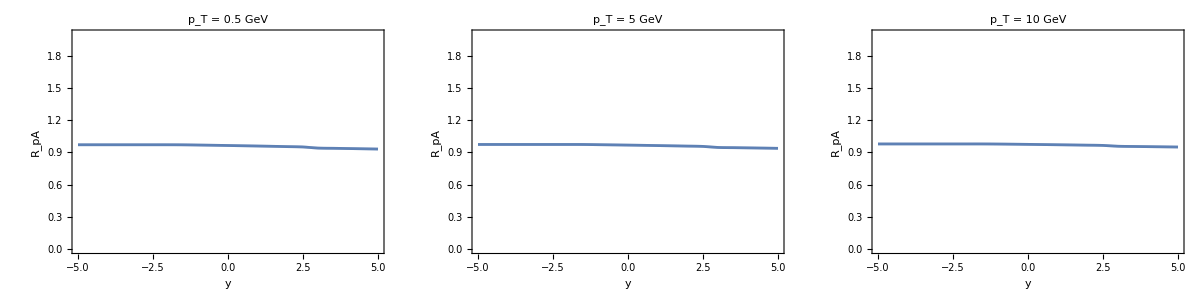

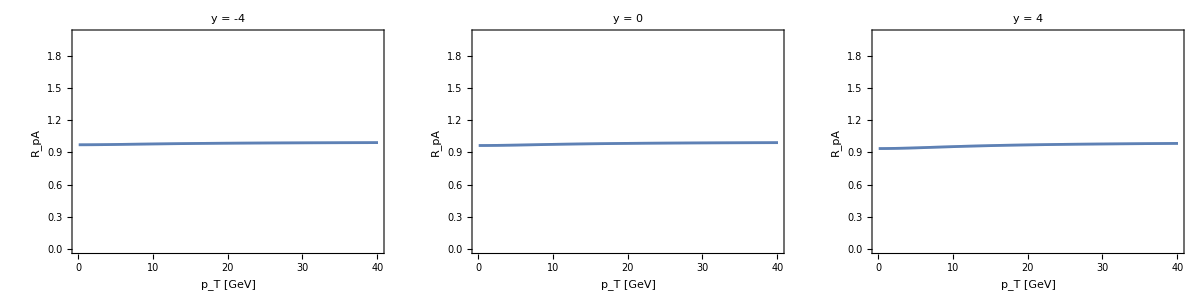

```mathematica
Grid[{{mypAPlotY[0.5],mypAPlotY[5],mypAPlotY[10]}}]
Grid[{{mypAPlotPT[-4],mypAPlotPT[0],mypAPlotPT[4]}}]
```

## RpA vs Rapidity (y) binned (pT averaged)

```mathematica
ptmin = 0.1;
ptmax = 20;
```

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultPTavg[{ymin_,ymax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ybins = -5 + 0.5Range[0,20]
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

```mathematica
binnedRPAelossVSY = RpAresultPTavg/@ Transpose[{Drop[ybins,-1],Drop[ybins,1]}];
```

```mathematica
binnedRPAElossDataVSY = Transpose[{Drop[ybins,-1],binnedRPAelossVSY}]
```

{{-5.,0.981885},{-4.5,0.981885},{-4.,0.981885},{-3.5,0.981885},{-3.,0.981885},{-2.5,0.981886},{-2.,0.981894},{-1.5,0.981656},{-1.,0.980764},{-0.5,0.979424},{0.,0.977993},{0.5,0.976466},{1.,0.974836},{1.5,0.973095},{2.,0.97143},{2.5,0.966944},{3.,0.962394},{3.5,0.960851},{4.,0.959403},{4.5,0.957624}}

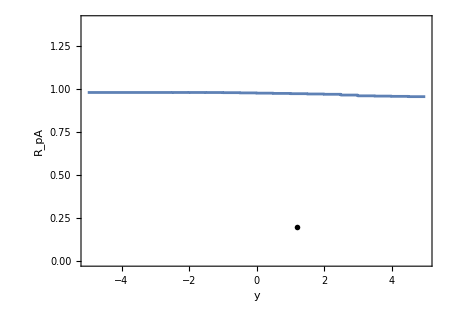

```mathematica
rapidityplot=ListStepPlot[binnedRPAElossDataVSY,Right,PlotRange->{{-5,5},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ptmin]<>"<$p_T$<"<>ToString[ptmax]<>" GeV }"],{1.2,0.2}]},FrameLabel->{"y","R_pA"}]
```

```mathematica
RpAresultPTavg[{-5,5}]
```

0.974804

## RpA vs p_T binned Plots (y averaged)

### Forward Rapidity (1 = 1.5 < y < 4, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{1.5,4},Length[myPTBins]]
```

{{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4},{1.5,4}}

```mathematica
ymax=myYBin1[[1,2]];
ymin=myYBin1[[1,1]];
```

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{1.5,4,0.,2.5},{1.5,4,2.5,5.},{1.5,4,5.,7.5},{1.5,4,7.5,10.},{1.5,4,10.,12.5},{1.5,4,12.5,15.},{1.5,4,15.,17.5},{1.5,4,17.5,20.},{1.5,4,20.,22.5},{1.5,4,22.5,25.},{1.5,4,25.,27.5},{1.5,4,27.5,30.},{1.5,4,30.,32.5},{1.5,4,32.5,35.},{1.5,4,35.,37.5},{1.5,4,37.5,40.},{1.5,4,40.,42.5},{1.5,4,42.5,45.},{1.5,4,45.,47.5},{1.5,4,47.5,50.}}

```mathematica
binnedRPAelossVSPT1 =RpAresultAvg/@myBins1
```

{0.94735,0.950167,0.95469,0.959705,0.964404,0.9685,0.971973,0.974917,0.977386,0.979465,0.981228,0.982737,0.984042,0.985179,0.986175,0.987052,0.987819,0.988413,0.98873,0.988666}

```mathematica
binnedRPAelossDataVSPT1  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT1}]
```

{{0.,0.94735},{2.5,0.950167},{5.,0.95469},{7.5,0.959705},{10.,0.964404},{12.5,0.9685},{15.,0.971973},{17.5,0.974917},{20.,0.977386},{22.5,0.979465},{25.,0.981228},{27.5,0.982737},{30.,0.984042},{32.5,0.985179},{35.,0.986175},{37.5,0.987052},{40.,0.987819},{42.5,0.988413},{45.,0.98873},{47.5,0.988666}}

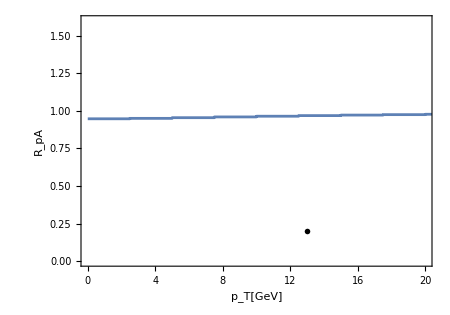

```mathematica
forwardplot= ListStepPlot[binnedRPAelossDataVSPT1,Right,PlotRange->{{0,20},{0,1.6}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_pA"}]
```

### Backward Rapidity (2 = -5 < y < -2.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-5,2.5},Length[myPTBins]]
```

{{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5},{-5,2.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-5,2.5,0.,2.5},{-5,2.5,2.5,5.},{-5,2.5,5.,7.5},{-5,2.5,7.5,10.},{-5,2.5,10.,12.5},{-5,2.5,12.5,15.},{-5,2.5,15.,17.5},{-5,2.5,17.5,20.},{-5,2.5,20.,22.5},{-5,2.5,22.5,25.},{-5,2.5,25.,27.5},{-5,2.5,27.5,30.},{-5,2.5,30.,32.5},{-5,2.5,32.5,35.},{-5,2.5,35.,37.5},{-5,2.5,37.5,40.},{-5,2.5,40.,42.5},{-5,2.5,42.5,45.},{-5,2.5,45.,47.5},{-5,2.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

2.5

-5

```mathematica
binnedRPAelossVSPT2 =RpAresultAvg/@myBins1
```

{0.967253,0.969016,0.971828,0.974887,0.977741,0.980225,0.982321,0.984066,0.985525,0.986755,0.987799,0.988692,0.988168,0.990351,0.990896,0.991398,0.99184,0.992218,0.992522,0.992743}

```mathematica
binnedRPAelossDataVSPT2  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT2}]
```

{{0.,0.967253},{2.5,0.969016},{5.,0.971828},{7.5,0.974887},{10.,0.977741},{12.5,0.980225},{15.,0.982321},{17.5,0.984066},{20.,0.985525},{22.5,0.986755},{25.,0.987799},{27.5,0.988692},{30.,0.988168},{32.5,0.990351},{35.,0.990896},{37.5,0.991398},{40.,0.99184},{42.5,0.992218},{45.,0.992522},{47.5,0.992743}}

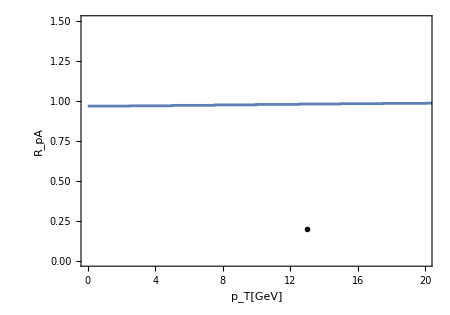

```mathematica
backwardplot=ListStepPlot[binnedRPAelossDataVSPT2,Right,PlotRange->{{0,20},{0,1.5}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_pA"}]
```

### Mid Rapidity (3 = -1.93 < y < -1.93, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-1.93,1.93},Length[myPTBins]]
```

{{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93},{-1.93,1.93}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-1.93,1.93,0.,2.5},{-1.93,1.93,2.5,5.},{-1.93,1.93,5.,7.5},{-1.93,1.93,7.5,10.},{-1.93,1.93,10.,12.5},{-1.93,1.93,12.5,15.},{-1.93,1.93,15.,17.5},{-1.93,1.93,17.5,20.},{-1.93,1.93,20.,22.5},{-1.93,1.93,22.5,25.},{-1.93,1.93,25.,27.5},{-1.93,1.93,27.5,30.},{-1.93,1.93,30.,32.5},{-1.93,1.93,32.5,35.},{-1.93,1.93,35.,37.5},{-1.93,1.93,37.5,40.},{-1.93,1.93,40.,42.5},{-1.93,1.93,42.5,45.},{-1.93,1.93,45.,47.5},{-1.93,1.93,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.93

-1.93

```mathematica
binnedRPAelossVSPT3 =RpAresultAvg/@myBins1
```

{0.965148,0.967103,0.97021,0.973564,0.97668,0.979381,0.98165,0.983522,0.985082,0.986393,0.987503,0.988449,0.989258,0.989953,0.990561,0.991096,0.991568,0.991991,0.992378,0.992744}

```mathematica
binnedRPAelossDataVSPT3  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT3}]
```

{{0.,0.965148},{2.5,0.967103},{5.,0.97021},{7.5,0.973564},{10.,0.97668},{12.5,0.979381},{15.,0.98165},{17.5,0.983522},{20.,0.985082},{22.5,0.986393},{25.,0.987503},{27.5,0.988449},{30.,0.989258},{32.5,0.989953},{35.,0.990561},{37.5,0.991096},{40.,0.991568},{42.5,0.991991},{45.,0.992378},{47.5,0.992744}}

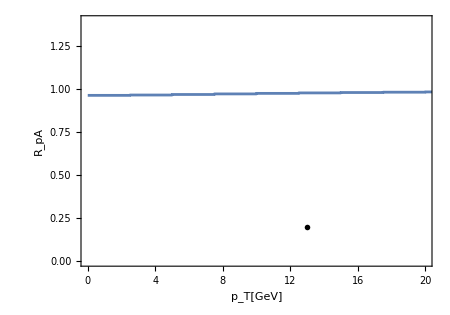

```mathematica
centralplot=ListStepPlot[binnedRPAelossDataVSPT3,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_pA"}]
```

### Back(4 = -2 < y < -1.5, averaged)

```mathematica
(*LogLogPlot[pAresult[0,pt]pt,{pt,ptmin,ptmax}]*)
```

```mathematica
RpAresultAvg[{ymin_,ymax_,ptmin_,ptmax_}] := NIntegrate[RpAresult[y,pt]*pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]/NIntegrate[pAresult[0,pt]*pt,{pt,ptmin,ptmax},{y,ymin,ymax}]
```

```mathematica
ptbins = 2.5Range[0,20]
```

{0.,2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.,37.5,40.,42.5,45.,47.5,50.}

```mathematica
myPTBins=Transpose[{Drop[ptbins,-1],Drop[ptbins,1]}]
```

{{0.,2.5},{2.5,5.},{5.,7.5},{7.5,10.},{10.,12.5},{12.5,15.},{15.,17.5},{17.5,20.},{20.,22.5},{22.5,25.},{25.,27.5},{27.5,30.},{30.,32.5},{32.5,35.},{35.,37.5},{37.5,40.},{40.,42.5},{42.5,45.},{45.,47.5},{47.5,50.}}

```mathematica
myYBin1=ConstantArray[{-2,1.5},Length[myPTBins]]
```

{{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5},{-2,1.5}}

```mathematica
myBins1=Flatten/@Partition[Riffle[myYBin1,myPTBins],2]
```

{{-2,1.5,0.,2.5},{-2,1.5,2.5,5.},{-2,1.5,5.,7.5},{-2,1.5,7.5,10.},{-2,1.5,10.,12.5},{-2,1.5,12.5,15.},{-2,1.5,15.,17.5},{-2,1.5,17.5,20.},{-2,1.5,20.,22.5},{-2,1.5,22.5,25.},{-2,1.5,25.,27.5},{-2,1.5,27.5,30.},{-2,1.5,30.,32.5},{-2,1.5,32.5,35.},{-2,1.5,35.,37.5},{-2,1.5,37.5,40.},{-2,1.5,40.,42.5},{-2,1.5,42.5,45.},{-2,1.5,45.,47.5},{-2,1.5,47.5,50.}}

```mathematica
ymax=myYBin1[[1,2]]
ymin=myYBin1[[1,1]]
```

1.5

-2

```mathematica
binnedRPAelossVSPT4 =RpAresultAvg/@myBins1
```

{0.966316,0.968205,0.971204,0.974435,0.977437,0.980039,0.982225,0.984026,0.985527,0.986789,0.987857,0.988768,0.989547,0.990215,0.9908,0.991314,0.991771,0.992199,0.992637,0.993123}

```mathematica
binnedRPAelossDataVSPT4  = Transpose[{Drop[ptbins,-1],binnedRPAelossVSPT4}]
```

{{0.,0.966316},{2.5,0.968205},{5.,0.971204},{7.5,0.974435},{10.,0.977437},{12.5,0.980039},{15.,0.982225},{17.5,0.984026},{20.,0.985527},{22.5,0.986789},{25.,0.987857},{27.5,0.988768},{30.,0.989547},{32.5,0.990215},{35.,0.9908},{37.5,0.991314},{40.,0.991771},{42.5,0.992199},{45.,0.992637},{47.5,0.993123}}

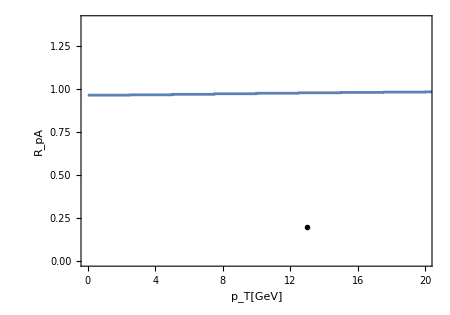

```mathematica
backplot=ListStepPlot[binnedRPAelossDataVSPT4,Right,PlotRange->{{0,20},{0,1.4}},Epilog->{Inset[myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}"<>"\\text{ = "<>cE<>" TeV, "<>ToString[ymin]<>"<y<"<>ToString[ymax]<>" }"],{13,0.2}]},FrameLabel->{"p_T[GeV]","R_pA"}]
```

## Read All Centrality Data

### Read All Centrality Data

```mathematica
centFile[cent_,particle_,kind_]:=Module[{base=FileNameJoin[{wd,"..","output",particle}],tag},tag="cent_"<>cent<>"_"<>particle;
Switch[kind,"pA",FileNameJoin[{base,tag<>"_pA-cross-section.tsv"}],"pp",FileNameJoin[{base,tag<>"_pp-cross-section.tsv"}],"RpA",FileNameJoin[{base,tag<>"_RpA.tsv"}]]]
```

```mathematica
loadCent[cent_String,particle_String:particle]:=Module[{pAraw,ppraw,RpAraw,pAlog,pAerrlog,pblog,rp,rperr,yb,ptb},If[!FileExistsQ/@centFile[cent,particle,#]&/@{"pA","pp","RpA"}//And@@#&,MessageDialog["Missing one or more files for centrality: "<>cent];
Return[$Failed];];
pAraw=Import[centFile[cent,particle,"pA"]];
ppraw=Import[centFile[cent,particle,"pp"]];
RpAraw=Import[centFile[cent,particle,"RpA"]];
(*exact same transforms you already use*)
pAlog=Interpolation[myLog/@pAraw[[All,{1,2,3}]],InterpolationOrder->Automatic];
pAerrlog=Interpolation[myLog/@pAraw[[All,{1,2,4}]],InterpolationOrder->Automatic];
pblog=Interpolation[myLog/@ppraw,InterpolationOrder->Automatic];
rp=Interpolation[RpAraw[[All,{1,2,3}]],InterpolationOrder->Automatic];
rperr=Interpolation[RpAraw[[All,{1,2,4}]],InterpolationOrder->Automatic];
{yb,ptb}={rp[[1,1]],rp[[1,2]]};(*{ymin,ymax},{ptmin,ptmax}*)
<|"centTag"->cent,"pA"->(Exp[pAlog[#1,#2]]&),"pAerr"->(Exp[pAerrlog[#1,#2]]&),"pp"->(Exp[pblog[#1,#2]]&),"RpA"->(rp[#1,#2]&),"RpAerr"->(rperr[#1,#2]&),"ymin"->yb[[1]],"ymax"->yb[[2]],"ptmin"->ptb[[1]],"ptmax"->ptb[[2]]|>];
```

```mathematica
centOne=loadCent[centrality];
centOne["RpA"][0,1.]
```

0.965186

```mathematica
dataByCent=AssociationMap[loadCent,centTags]
```

<|0-20→<|centTag→0-20,pA→(Exp[pAlog$3486991[#1,#2]]&),pAerr→(Exp[pAerrlog$3486991[#1,#2]]&),pp→(Exp[pblog$3486991[#1,#2]]&),RpA→(rp$3486991[#1,#2]&),RpAerr→(rperr$3486991[#1,#2]&),ymin→-5.,ymax→5.,ptmin→0.1,ptmax→40.1|>,20-40→<|centTag→20-40,pA→(Exp[pAlog$3487109[#1,#2]]&),pAerr→(Exp[pAerrlog$3487109[#1,#2]]&),pp→(Exp[pblog$3487109[#1,#2]]&),RpA→(rp$3487109[#1,#2]&),RpAerr→(rperr$3487109[#1,#2]&),ymin→-5.,ymax→5.,ptmin→0.1,ptmax→40.1|>,40-60→<|centTag→40-60,pA→(Exp[pAlog$3487227[#1,#2]]&),pAerr→(Exp[pAerrlog$3487227[#1,#2]]&),pp→(Exp[pblog$3487227[#1,#2]]&),RpA→(rp$3487227[#1,#2]&),RpAerr→(rperr$3487227[#1,#2]&),ymin→-5.,ymax→5.,ptmin→0.1,ptmax→40.1|>,60-100→<|centTag→60-100,pA→(Exp[pAlog$3487345[#1,#2]]&),pAerr→(Exp[pAerrlog$3487345[#1,#2]]&),pp→(Exp[pblog$3487345[#1,#2]]&),RpA→(rp$3487345[#1,#2]&),RpAerr→(rperr$3487345[#1,#2]&),ymin→-5.,ymax→5.,ptmin→0.1,ptmax→40.1|>|>

```mathematica
Keys[dataByCent]
```

{0-20,20-40,40-60,60-100}

```mathematica
plotRpA3D[cent_]:=Module[{ymin=cent["ymin"],ymax=cent["ymax"],ptmin=cent["ptmin"],ptmax=cent["ptmax"]},Show[Plot3D[cent["RpA"][y,pt],{y,ymin,ymax},{pt,ptmin,ptmax},PlotRange->{0,1.5}],Plot3D[1,{y,ymin,ymax},{pt,ptmin,ptmax},PlotStyle->Opacity[0.5,Red],Mesh->None]]]
```

```mathematica
plotYslice[cent_,pt_?NumericQ]:=Module[{ymin=cent["ymin"],ymax=cent["ymax"]},With[{f=cent["RpA"],e=cent["RpAerr"]},Plot[{f[y,pt],f[y,pt]-e[y,pt],f[y,pt]+e[y,pt]},{y,ymin,ymax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["p_T = "<>ToString[pt]<>" GeV",18],FrameLabel->{"y",Subscript["R","pA"]},ImageSize->400,PlotRange->{0,2.0}]]]
```

```mathematica
plotPTslice[cent_,y_?NumericQ]:=Module[{ptmin=cent["ptmin"],ptmax=cent["ptmax"]},With[{f=cent["RpA"],e=cent["RpAerr"]},Plot[{f[y,pt],f[y,pt]-e[y,pt],f[y,pt]+e[y,pt]},{pt,ptmin,ptmax},PlotStyle->{plotColor1,{Opacity[0.1],plotColor1},{Opacity[0.1],plotColor1}},Filling->{2->{3}},PlotLabel->Style["y = "<>ToString[y],18],FrameLabel->{Subscript["p","T"]~MaTeX`MaTeX~" [GeV]",Subscript["R","pA"]},ImageSize->400,PlotRange->{0,2.0}]]]
```

-Graphics3D-

-Graphics-

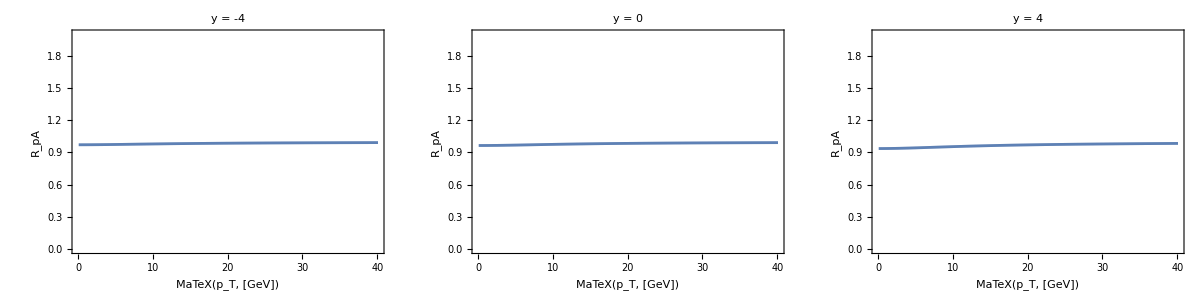

```mathematica
plotRpA3D[centOne]
Grid[{{plotYslice[centOne,0.5],plotYslice[centOne,5],plotYslice[centOne,10]}}]
Grid[{{plotPTslice[centOne,-4],plotPTslice[centOne,0],plotPTslice[centOne,4]}}]
```

```mathematica
(*----------STEP 4:Generalized averages----------*)
ClearAll[meanRpAOverY,meanRpAOverPT,meanRpAOverYandPT];
(*y-binned,pT-averaged over[pt1,pt2]*)
meanRpAOverY[cent_,{y1_,y2_},{pt1_,pt2_}]:=Module[{f=cent["RpA"],w=(cent["pA"][0,#]*#)&},NIntegrate[f[y,pt]*w[pt],{y,y1,y2},{pt,pt1,pt2}]/NIntegrate[w[pt],{y,y1,y2},{pt,pt1,pt2}]];

(*pT-binned,y-averaged over[y1,y2]*)
meanRpAOverPT[cent_,{y1_,y2_},{pt1_,pt2_}]:=Module[{f=cent["RpA"],w=(cent["pA"][0,#]*#)&},NIntegrate[f[y,pt]*w[pt],{pt,pt1,pt2},{y,y1,y2}]/NIntegrate[w[pt],{pt,pt1,pt2},{y,y1,y2}]];

(*full-range average (for RpA vs centrality)*)
meanRpAOverYandPT[cent_,{y1_,y2_},{pt1_,pt2_}]:=Module[{f=cent["RpA"],w=(cent["pA"][0,#]*#)&},NIntegrate[f[y,pt]*w[pt],{y,y1,y2},{pt,pt1,pt2}]/NIntegrate[w[pt],{y,y1,y2},{pt,pt1,pt2}]];
```

```mathematica
ptmin=0.1;ptmax=20;
meanRpAOverYandPT[centOne,{-5,5},{ptmin,ptmax}]
```

0.974804

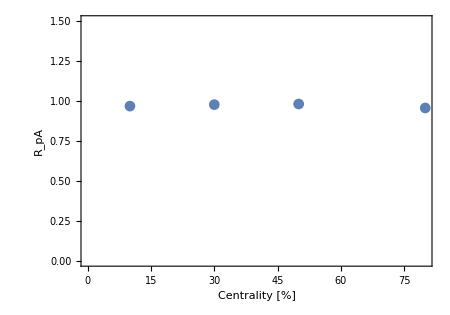

```mathematica
(*----------STEP 5:RpA vs Centrality----------*)
ClearAll[rpaVsCentrality];
rpaVsCentrality[data_Association,yRange_:{-4.5,4},ptRange_:{0.1,20}]:=Module[{pairs,mids,vals},pairs=centBins;(*{{0,20},{20,40},...} from your setup*)mids=Mean/@pairs;(*x-axis:bin midpoints*)vals=meanRpAOverYandPT[#,yRange,ptRange]&/@(data/@centTags);
Transpose[{mids,vals}]];
rpaCentData=rpaVsCentrality[dataByCent,{-4.5,4},{0.1,20}];
meanRpAErrOverYandPT[cent_,{y1_,y2_},{pt1_,pt2_}]:=Module[{e=cent["RpAerr"],w=(cent["pA"][0,#]*#)&},Sqrt[NIntegrate[(e[y,pt]^2)*w[pt],{y,y1,y2},{pt,pt1,pt2}]/NIntegrate[w[pt],{y,y1,y2},{pt,pt1,pt2}]]]
rpaVsCentralityWithErr[data_Association,yRange_:{-5,5},ptRange_:{0.1,20}]:=Module[{pairs=centBins,mids,halfWidths,cents,vals,errs},mids=Mean/@pairs;(*x positions*)halfWidths=(#[[2]]-#[[1]])/2&/@pairs;(*horizontal half-widths*)cents=data/@centTags;(*bundles by centrality tag*)vals=meanRpAOverYandPT[#,yRange,ptRange]&/@cents;
errs=meanRpAErrOverYandPT[#,yRange,ptRange]&/@cents;
<|"x"->mids,"y"->vals,"dy"->errs,"dx"->halfWidths|>];
rpaCent=rpaVsCentralityWithErr[dataByCent,{-4.5,4},{0.1,20}];
ListPlot[rpaCentData,PlotRange->{0,1.5},Frame->True,FrameLabel->{"Centrality [%]",Subscript["R","pA"]},PlotMarkers->Automatic]
```

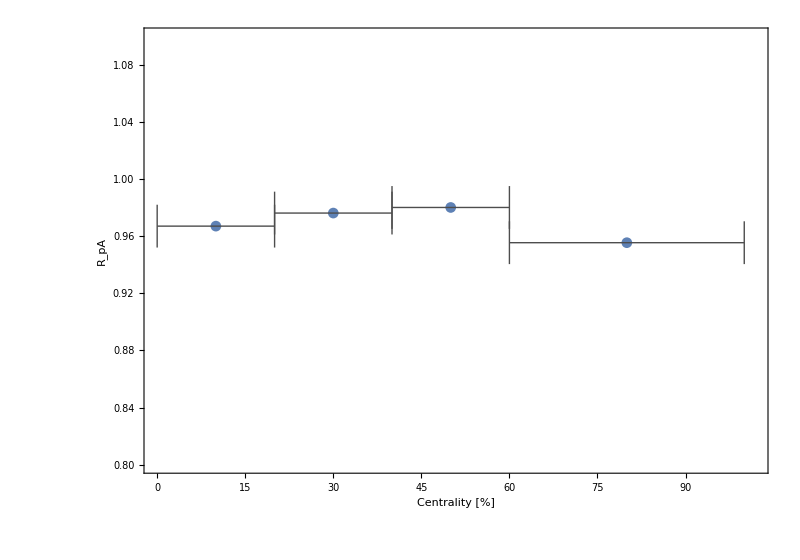

```mathematica
(*----------REPLACE your ListPlot with this----------*)
RpavsCent=With[{pts=Transpose[{rpaCent["x"],MapThread[Around,{rpaCent["y"],rpaCent["dy"]}]}],x=rpaCent["x"],y=rpaCent["y"],dx=rpaCent["dx"]},ListPlot[pts,PlotMarkers->Automatic,Frame->True,PlotRange->{{-0.2,102},{0.8,1.1}},FrameLabel->{"Centrality [%]",Subscript["R","pA"]},ImageSize->800,Epilog->Table[{GrayLevel[0.3],Thick,Line[{{x[[i]]-dx[[i]],y[[i]]},{x[[i]]+dx[[i]],y[[i]]}}],Line[{{x[[i]]-dx[[i]],y[[i]]-0.015},{x[[i]]-dx[[i]],y[[i]]+0.015}}],Line[{{x[[i]]+dx[[i]],y[[i]]-0.015},{x[[i]]+dx[[i]],y[[i]]+0.015}}]},{i,Length[x]}]]]
```

```mathematica
Export[wd<>"/figures/RpA_vs_centrality.pdf",RpavsCent]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/figures/RpA_vs_centrality.pdf

```mathematica
(*----------STEP 6A:RpA(y) with pT-averaging,binned in y----------*)
ClearAll[binnedRpAvsYPlot];
binnedRpAvsYPlot[cent_,yEdges_List,ptRange_:{0.1,20}]:=Module[{bins=Transpose[{Drop[yEdges,-1],Drop[yEdges,1]}],vals,data},vals=meanRpAOverY[cent,#,ptRange]&/@bins;
data=Transpose[{Drop[yEdges,-1],vals}];
ListStepPlot[data,Right,PlotRange->{{Min[yEdges],Max[yEdges]},{0.8,1.2}},ImageSize->800,Epilog->{Inset[Column[{myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}\\,\\text{ = "<>cE<>" TeV}"],myMaTeX[ToString[ptRange[[1]]]<>" < p_T < "<>ToString[ptRange[[2]]]<>"\\text{ GeV}"],myMaTeX["\\text{Centrality: }"<>Lookup[cent,"centTag",""]<>"\\%"]},Spacings->0.5],{0.35 Max[yEdges],1.1}]},FrameLabel->{"y",Subscript["R","pA"]}]];
ybins=-5+0.5 Range[0,20];
```

```mathematica
yplot=GraphicsGrid[{{binnedRpAvsYPlot[dataByCent["0-20"],ybins,{0.1,20}],binnedRpAvsYPlot[dataByCent["20-40"],ybins,{0.1,20}]},{binnedRpAvsYPlot[dataByCent["40-60"],ybins,{0.1,20}],binnedRpAvsYPlot[dataByCent["60-100"],ybins,{0.1,20}]}},ImageSize->1200]
```

NIntegrate::inumr: The integrand ⅇ^(Interpolation[Symbol[],InterpolationOrder→Automatic][0,pt]) pt Interpolation[Symbol[],InterpolationOrder→Automatic][y,pt] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-5.,-4.5},{0.1,20}}.

NIntegrate::inumr: The integrand ⅇ^(Interpolation[Symbol[],InterpolationOrder→Automatic][0,pt]) pt has evaluated to non-numerical values for all sampling points in the region with boundaries {{-5.,-4.5},{0.1,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
Export[wd<>"/figures/y_plot_centrality.pdf",yplot]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/figures/y_plot_centrality.pdf

```mathematica
(*----------STEP 6B:RpA(pT) with y-averaging,binned in pT----------*)
ClearAll[binnedRpAvsPTPlot];
binnedRpAvsPTPlot[cent_,yRange:{_,_},ptEdges_List]:=Module[{ptBins=Transpose[{Drop[ptEdges,-1],Drop[ptEdges,1]}],vals,data},vals=meanRpAOverPT[cent,yRange,#]&/@ptBins;
data=Transpose[{Drop[ptEdges,-1],vals}];
ListStepPlot[data,Right,PlotRange->{{Min[ptEdges],20},{0.6,1.1}},Epilog->{Inset[Column[{myMaTeX["\\boldsymbol{\\sqrt{s_{\\rm NN}}}\\,\\text{ = "<>cE<>" TeV}"],myMaTeX[ToString[yRange[[1]]]<>" < y < "<>ToString[yRange[[2]]]],myMaTeX["\\text{Centrality: }"<>Lookup[cent,"centTag",""]<>"\\%"]},Spacings->0.5],{0.7*20,0.8}]},FrameLabel->{"p_T [GeV]",Subscript["R","pA"]}]];
(*Example ranges matching your forward/mid/back choices*)
ptEdges=2.5 Range[0,20];
```

```mathematica
(*binnedRpAvsPTPlot[dataByCent["60-100"],{-5,-2.5},ptEdges]  (*backward-1*)*)
```

```mathematica
pTplotMidRapRap = GraphicsGrid[{{binnedRpAvsPTPlot[dataByCent["0-20"],{-1.93,1.93},ptEdges] ,binnedRpAvsPTPlot[dataByCent["20-40"],{-1.93,1.93},ptEdges] },{binnedRpAvsPTPlot[dataByCent["40-60"],{-1.93,1.93},ptEdges] ,binnedRpAvsPTPlot[dataByCent["60-100"],{-1.93,1.93},ptEdges] }},ImageSize->1200]
```

-Graphics-

```mathematica
Export[wd<>"/figures/pt_plot_MidRap_Diffcentrality.pdf",pTplotMidRapRap ]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/figures/pt_plot_MidRap_Diffcentrality.pdf

```mathematica
pTplotForwardRapRap = GraphicsGrid[{{binnedRpAvsPTPlot[dataByCent["0-20"],{1.5,4},ptEdges] ,binnedRpAvsPTPlot[dataByCent["20-40"],{1.5,4},ptEdges] },{binnedRpAvsPTPlot[dataByCent["40-60"],{1.5,4},ptEdges] ,binnedRpAvsPTPlot[dataByCent["60-100"],{1.5,4},ptEdges] }},ImageSize->1200]
```

-Graphics-

```mathematica
Export[wd<>"/figures/pt_plot_ForwardRap_Diffcentrality.pdf",pTplotForwardRapRap]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/figures/pt_plot_ForwardRap_Diffcentrality.pdf

```mathematica
pTplotBackwardRapRap = GraphicsGrid[{{binnedRpAvsPTPlot[dataByCent["0-20"],{-4.5,-2.5},ptEdges] ,binnedRpAvsPTPlot[dataByCent["20-40"],{-4.5,-2.5},ptEdges] },{binnedRpAvsPTPlot[dataByCent["40-60"],{-4.5,-2.5},ptEdges] ,binnedRpAvsPTPlot[dataByCent["60-100"],{-4.5,-2.5},ptEdges] }},ImageSize->1200]
```

-Graphics-

```mathematica
Export[wd<>"/figures/pt_plot_BackwardRap_Diffcentrality.pdf",pTplotBackwardRapRap  ]
```

/home/sawin/Desktop/Charmonia/quenching_integration/data_analysis/figures/pt_plot_BackwardRap_Diffcentrality.pdf